Solution to general 4 state model with forward k rates and reverse r rates

```mathematica
ass={km>0, kp>0, kon>0, c0<c1, c1>0, c0>0, koff>0 };
```

```mathematica
FullSimplify[Solve[{J,J,J,J,1}=={k1 p1 - r1 p2, k2 p2 - r2 p3, k3 p3 - r3 p4, k4 p4 - r4 p1, p1+p2+p3+p4}, {J, p1,p2,p3,p4}]]
```

{{J→(k1 k2 k3 k4-r1 r2 r3 r4)/(k2 k3 k4+k4 r1 (k3+r2)+r1 r2 r3+k1 (k4 (k3+r2)+r2 r3+k2 (k3+k4+r3))+r1 (k3+r2) r4+(r1+r2) r3 r4+k2 (k3+r3) r4),p1→(k2 k3 k4+k3 k4 r1+r1 r2 (k4+r3))/(k2 k3 k4+k4 r1 (k3+r2)+r1 r2 r3+k1 (k4 (k3+r2)+r2 r3+k2 (k3+k4+r3))+r1 (k3+r2) r4+(r1+r2) r3 r4+k2 (k3+r3) r4),p2→(k1 k4 (k3+r2)+k1 r2 r3+r2 r3 r4)/(k2 k3 k4+k4 r1 (k3+r2)+r1 r2 r3+k1 (k4 (k3+r2)+r2 r3+k2 (k3+k4+r3))+r1 (k3+r2) r4+(r1+r2) r3 r4+k2 (k3+r3) r4),p3→(k1 k2 (k4+r3)+(k2+r1) r3 r4)/(k2 k3 k4+k4 r1 (k3+r2)+r1 r2 r3+k1 (k4 (k3+r2)+r2 r3+k2 (k3+k4+r3))+r1 (k3+r2) r4+(r1+r2) r3 r4+k2 (k3+r3) r4),p4→(k1 k2 k3+k2 k3 r4+r1 (k3+r2) r4)/(k2 k3 k4+k4 r1 (k3+r2)+r1 r2 r3+k1 (k4 (k3+r2)+r2 r3+k2 (k3+k4+r3))+r1 (k3+r2) r4+(r1+r2) r3 r4+k2 (k3+r3) r4)}}

```mathematica
sol = {{J->(k1 k2 k3 k4-r1 r2 r3 r4)/(k2 k3 k4+k4 r1 (k3+r2)+r1 r2 r3+k1 (k4 (k3+r2)+r2 r3+k2 (k3+k4+r3))+k2 (k3+r3) r4+(r1 (k3+r2)+(r1+r2) r3) r4),p1->(k2 k3 k4+k3 k4 r1+r1 r2 (k4+r3))/(k2 k3 k4+k4 r1 (k3+r2)+r1 r2 r3+k1 (k4 (k3+r2)+r2 r3+k2 (k3+k4+r3))+k2 (k3+r3) r4+(r1 (k3+r2)+(r1+r2) r3) r4),p2->(k1 k4 (k3+r2)+k1 r2 r3+r2 r3 r4)/(k2 k3 k4+k4 r1 (k3+r2)+r1 r2 r3+k1 (k4 (k3+r2)+r2 r3+k2 (k3+k4+r3))+k2 (k3+r3) r4+(r1 (k3+r2)+(r1+r2) r3) r4),p3->(k1 k2 (k4+r3)+(k2+r1) r3 r4)/(k2 k3 k4+k4 r1 (k3+r2)+r1 r2 r3+k1 (k4 (k3+r2)+r2 r3+k2 (k3+k4+r3))+k2 (k3+r3) r4+(r1 (k3+r2)+(r1+r2) r3) r4),p4->(k1 k2 k3+(k2 k3+r1 (k3+r2)) r4)/(k2 k3 k4+k4 r1 (k3+r2)+r1 r2 r3+k1 (k4 (k3+r2)+r2 r3+k2 (k3+k4+r3))+k2 (k3+r3) r4+(r1 (k3+r2)+(r1+r2) r3) r4)}};
```

our specific system

```mathematica
FullSimplify[sol/.{k1-> kp, r1->  b km, k3-> km, r3-> kp, k2-> c kon, r2-> koff, k4-> koff, r4-> c kon}]
```

{{J→-((-1+b) c km koff kon kp)/((koff+c kon) (c kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp))),p1→(km koff (c kon+b (km+koff+kp)))/((koff+c kon) (c kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp))),p2→(koff kp (km+koff+c kon+kp))/((koff+c kon) (c kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp))),p3→(c kon kp (b km+koff+c kon+kp))/((koff+c kon) (c kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp))),p4→(c km kon (b (km+koff)+c kon+kp))/((koff+c kon) (c kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp)))}}

```mathematica
p4c[c_]:=(c km kon)/((koff+c kon) (km+kp));
```

```mathematica
p4cb[c_]:=(c km kon (b (km+koff)+c kon+kp))/((koff+c kon) (c kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp)))
```

```mathematica
Simplify[p4c[c1]/p4c[c0]]
```

```mathematica
(c1 (koff+c0 kon))/(c0 (koff+c1 kon))/.c1-> c0 E^A
```

(ⅇ^A (koff+c0 kon))/(koff+c0 ⅇ^A kon)

```mathematica
FullSimplify[p4c[c1]/p4c[c0]]
```

```mathematica
(c1 (koff+c0 kon))/(c0 (koff+c1 kon))
```

```mathematica
FullSimplify[((c1 koff (km+koff+c0 kon)+c1 (koff+2 c0 kon) kp)/(c0 koff (km+koff+c1 kon)+c0 (koff+2 c1 kon) kp))^2==(c1 (b km koff (km+koff+kp)+koff kp (km+koff+kp)+c0 kon (km+kp) (koff+2 kp)))/(c0 (b km koff (km+koff+kp)+koff kp (km+koff+kp)+c1 kon (km+kp) (koff+2 kp)))]
```

sweeping large paramter range

```mathematica
rv1= Table[{ c0->  10^RandomReal[{-2,-2}],kp->  10^RandomReal[{-2,2}],km->  10^RandomReal[{-2,2}],kon->  10^RandomReal[{-2,2}],koff->  10^RandomReal[{-2,2}] }, {10000}];
```

```mathematica
rvals=Table[AppendTo[rv1[[j]], c1->10^RandomReal[{Log10[c0/.rv1[[j]]],0} ]], {j,1,Length[rv1]}];
```

```mathematica
rvals[[45]]
```

{c0→0.01,kp→6.79613,km→0.0215608,kon→0.0343566,koff→0.977443,c1→0.0671254}

```mathematica
Simplify[Solve[D[(c1 (koff+c0 kon) (b (km+koff)+c1 kon+kp) (c0 kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp)))/(c0 (koff+c1 kon) (b (km+koff)+c0 kon+kp) (c1 kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp))),b]==0,b],ass]
```

{{b→(km^3+km koff (koff+kp)+km^2 (2 koff+kp)-√(km (km+koff) (km+kp) (km+koff+kp) (km+koff+c0 kon+kp) (km+koff+c1 kon+kp)))/(km (km+koff) (km+koff+kp))},{b→(km^3+km koff (koff+kp)+km^2 (2 koff+kp)+√(km (km+koff) (km+kp) (km+koff+kp) (km+koff+c0 kon+kp) (km+koff+c1 kon+kp)))/(km (km+koff) (km+koff+kp))}}

```mathematica
bm = (km^3+km koff (koff+kp)+km^2 (2 koff+kp)+√(km (km+koff) (km+kp) (km+koff+kp) (km+koff+c0 kon+kp) (km+koff+c1 kon+kp)))/(km (km+koff) (km+koff+kp));
```

```mathematica
fm  = (c1 (koff+c0 kon) (b (km+koff)+c1 kon+kp) (c0 kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp)))/(c0 (koff+c1 kon) (b (km+koff)+c0 kon+kp) (c1 kon (km+kp)+b km (km+koff+kp)+kp (km+koff+kp)))/5/.b-> bm;
```

```mathematica
bmsweep = Table[{Log[c1/c0]/.rvals[[i]], fm/.rvals[[i]]}, {i,1,Length[rvals]}];
```

```mathematica
bmsweep[[1]]
```

{3.65867,25.8798}

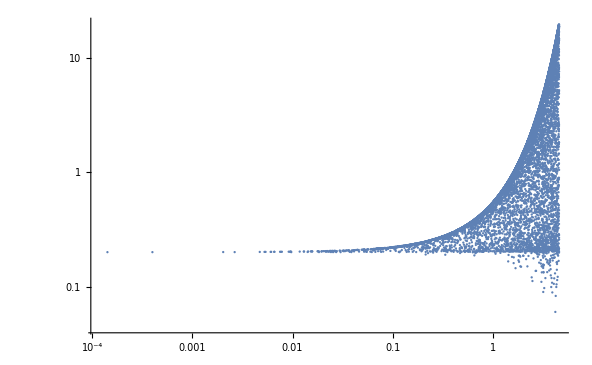

```mathematica
ListLogLogPlot[bmsweep, PlotRange->All]
```

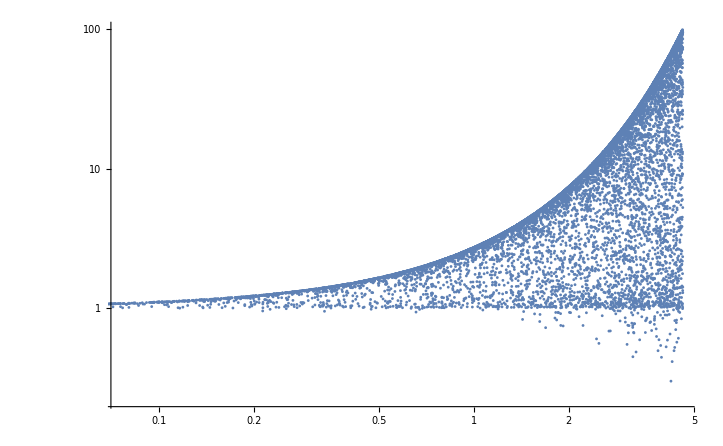

```mathematica
Show[ListLogLogPlot[bmsweep], LogLog
```